Část na parametry

```mathematica
h = 1
V =1
```

1

1

```mathematica
x1 = 1
```

1

```mathematica
x2=0
```

0

Část na výpočet βstart, βend a čas

```mathematica
X2 = h(1/(Cos[B])-1/(Cos[β]))
```

Sec[B]-Sec[β]

```mathematica
X1 = h(1/2Log[(Cos[B/2]+Sin[B/2])/(Cos[B/2]-Sin[B/2])]-1/2Log[(Cos[β/2]+Sin[β/2])/(Cos[β/2]-Sin[β/2])]+(1/(Cos[β])-1/(Cos[B]))(Sin[B])/(Cos[B]))
```

1/2 Log[(Cos[B/2]+Sin[B/2])/(Cos[B/2]-Sin[B/2])]-1/2 Log[(Cos[β/2]+Sin[β/2])/(Cos[β/2]-Sin[β/2])]+(-Sec[B]+Sec[β]) Tan[B]

```mathematica
res = FindRoot[{X1==x1,X2==x2},{{B,-1},{β,1}}]
```

{B→0.865769,β→-0.865769}

```mathematica
βstart = B /.res
```

0.865769

```mathematica
βend = β /. res
```

-0.865769

```mathematica
t1 = -(h/V)(Tan[βstart]-Tan[βend])
```

-2.3504

Kontrolní část

```mathematica
h(1/(Cos[βstart])-1/(Cos[βend]))
```

0.

```mathematica
h(1/2Log[(Cos[βstart/2]+Sin[βstart/2])/(Cos[βstart/2]-Sin[βstart/2])]-1/2Log[(Cos[βend/2]+Sin[βend/2])/(Cos[βend/2]-Sin[βend/2])]+(1/(Cos[βend])-1/(Cos[βstart]))(Sin[βstart])/(Cos[βstart]))
```

1.

```mathematica
rce = {x'[t]==V*Cos[β[t]]-(V/h)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h)(Cos[β[t]])^2}
```

{x'[t]==Cos[β[t]]-y[t],y'[t]==Sin[β[t]],β'[t]==Cos[β[t]]^2}

```mathematica
sol1 = NDSolve[Join[rce,{x[0]==x1,y[0]==x2,β[0]==βstart}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
{x[t],y[t]}/.sol1
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

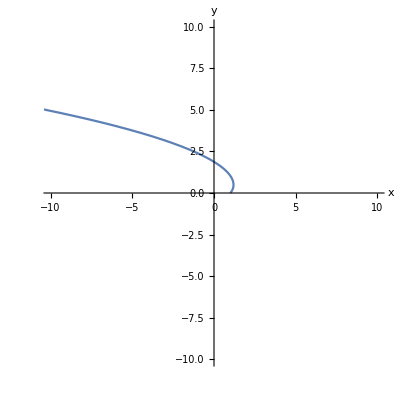

```mathematica
ParametricPlot[Table[{x[t],y[t]}/.sol1],{t,0,10},AxesLabel->{x,y},PlotRange->{{-10,10},{-10,10}}]
```